# 26: Hessenberg Reduction:

We know the standard way to do QR.  Work your way through the columns of the matrix choosing v according to the fairly simple recipe in lecture 10 and make zeros using the Householder reflection H=I-2v⊗v until you run out of columns! The reason for doing this was to reduce A.x=b to a simpler triangular form.

We are going systematically make zeros using Householder reflections in a similarity transformation
	A->Q.A.Qᵀ	
that preserve eigenvalues.  The reason for doing this is to reduce A to a simpler form: eventually one that just lets you read the eigenvalues of the diagonal!

## Optimistic Attempt

The plan is to make zeros in a matrix while not changing the eigenvalues!  To preserve the eigenvalues we need to use a similarity transformation
	A⟶Y.A.Y^-1
Since we are going to do a lot of matrix operations it is crucial that we use orthogonal similarity transformations
	A⟶Q.A.Qᵀ.
As an experiment we will see what happens if we try to zero an entire column and leave only the top element like we did before using our householder Q. Since the Householder Q is symmetric the Qᵀ=Q on the right does the same operations on the columns as Q on the left does on the rows.  As a result, similarity transformation destroys the zeros that were created in Q.A.

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
a1=A⟦All,1⟧;
Q=HouseMat[a1];
QA=Q.A; QAQtr=QA.Q;
TabView[{
"Q.A"->MatrixPlot[Chop[QA]],
"Q.A.Qᵀ"->MatrixPlot[Chop[QAQtr]]}]
```

12

This does not make zeros! It does however usually make matrices more Upper Triangular. The norm of strictly lower triangular portion divided by the norm of the entire thing is a reasonable way to measure degree of UTness!  We are going to use the Frobenius norm and note that since H is orthogonal the norm is unchanged by the similarity transformation!

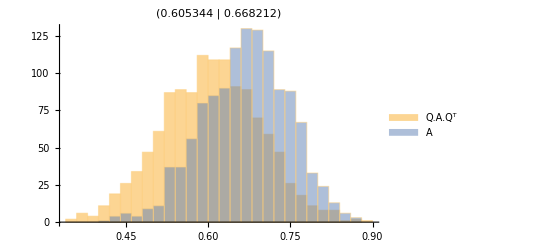

```mathematica
m=6;
SampleSize=1234;
Data=Table[
A=RandomReal[{-1,1},{m,m}];
a1=A⟦All,1⟧;
Q=HouseMat[a1];
QA=Q.A; QAQtr=QA.Qᵀ;
Map[Norm[LowerTriangularize[#,-1],"Frobenius"]&,{QAQtr,A}],
{SampleSize}]/Norm[A,"Frobenius"];
Histogram[Dataᵀ,20,ChartLegends->{"Q.A.Qᵀ","A"},PlotLabel->{Map[Mean,Dataᵀ]}]
```

We will come back to this!  For right now we want to make zeros that stay zeros!

## Realistic Attempt: Hessenberg Decomposition

The plan is to make zeros in a matrix while not changing the eigenvalues!  To preserve the eigenvalues we need to use a similarity transformation
	A⟶Y.A.Y^-1
Since we are going to do a lot of matrix operations it is crucial that we use orthogonal similarity transformations
	A⟶Q.A.Qᵀ.
As we saw zeroing the whole column (except the top element) is too greedy. However, if we try to zero everything except the top two elements we get zeros that are preserved.

This goes something like this.  Note that the H on the right makes zeros in the first column using rows 2 and above. It does not touch the first row! As a result, the Hᵀ=H on the left does not touch the first column and preserves the zeros that were just introduced!

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
a1=A⟦All,1⟧;
v=Join[{0},HouseVec[a1⟦2;;-1⟧]];
Q=IdentityMatrix[m]-2 KroneckerProduct[v,v];
QA=Q.A; QAQtr=QA.Qᵀ;
TabView[{
"Q"->MatrixPlot[Q],
"Q.A"->MatrixPlot[Chop[QA]],
"Q.A.Qᵀ"->MatrixPlot[Chop[QAQtr]]}]
```

123

Sweeping down the columns in a loop produces an almost upper triangular matrix with a single lower diagonal.  Accumulating these reflections into a single orthogonal matrix Q gives a decomposition
	A=Q.H.Qᵀ
where the inner matrix is upper triangular with one extra non-zero lower diagonal.  The inner matrix is called a Hessenberg matrix.

The eigenvalues of H are the same as the eigenvalues of A.  You do not build the orthogonal Q unless you need the eigenvectors.  in fact, you never need to build the Householder matrices.  This is a Mathematica implementation of algorithm 26.1.

```mathematica
HessenbergReduction[AIn_]:= Module[{A=AIn, m=Length[AIn],v,x},
Do[
x=A⟦k+1;;m,k⟧;
v=x; v⟦1⟧=v⟦1⟧+Sign[x⟦1⟧]*Norm[x];
v=Normalize[v];
A⟦k+1;;m,k;;m⟧=A⟦k+1;;m,k;;m⟧-2 KroneckerProduct[v,v.A⟦k+1;;m,k;;m⟧];
A⟦1;;m,k+1;;m⟧=A⟦1;;m,k+1;;m⟧-2 KroneckerProduct[A⟦1;;m,k+1;;m⟧.v,v],
{k,1,m-2}];
Chop[A]]
```

As always test.

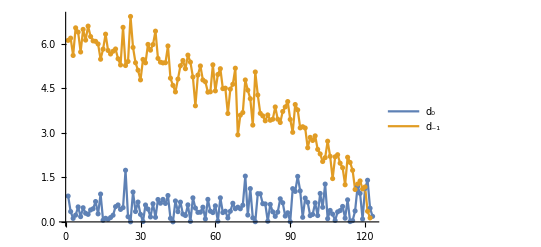

```mathematica
m=123;
A=RandomReal[{-1,1},{m,m}];
H=HessenbergReduction[A];
{λA,λH}=Map[Eigenvalues,{A,H}];
TableForm[{λA,λH}];
MatrixPlot[H,PlotLabel->Norm[λA-λH]];
ListPlot[Abs[{Diagonal[H,0],Diagonal[H,-1]}],
Joined->True,Mesh->All, PlotLegends->{"d_0","d_-1"}]
```

If Q is needed as well we can accumulate the Q just like in the QR algorithm.  Every linear algebra tool has a Hessenberg reduction command.   In Mathematica the command is HessenbergDecomposition and it give H and Q.

## Symmetric Hessenberg Decomposition

The question is what happens if we run the Hessenberg decomposition on a symmetric matrix. Since all the operations preserve symmetry we get a Symmetric tri-diagonal matrix which can be stored as two vectors!

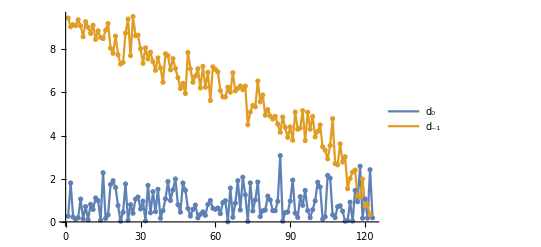

```mathematica
m=123;
S=RandomReal[{-1,1},{m,m}];S=S+Sᵀ;
T = Chop[HessenbergDecomposition[S]⟦2⟧];
MatrixPlot[T];
ListPlot[Abs[{Diagonal[T,0],Diagonal[T,-1]}],
Joined->True,Mesh->All, PlotLegends->{"d_0","d_-1"}]
```

## From Lecture 10: Householder Reflection Code

### Householder Reflections Matrix Functions

If v is a unit vector parallel to 
	sign(a⟦1⟧)||a||e_1+a
then the orthogonal matrix Q=I-2 v⊗v satisfies
	Q.a=||a||e_1
In other words, Q rotates the vector a to align with the vector e_1.

```mathematica
HouseVec[a_]:= Module[{v=a},
v⟦1⟧+=Sign[a⟦1⟧]Norm[a];
v/Norm[v]]
HouseMat[a_]:= Module[{v},
v=HouseVec[a];
IdentityMatrix[Length[a]]-2 KroneckerProduct[v,v]]
```

```mathematica
m=21;
a=RandomReal[{-1,1},m];
Q=HouseMat[a];
Norm[Q.Qᵀ -IdentityMatrix[m]]
Chop[Q.a]
```

4.46272×10^-16

{2.88227,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Householder Reflections Action Functions

There is no need to build the Householder matrix.  All we need to be able to do is apply the matrix to a vector x.

```mathematica
HouseActionVec[x_,a_]:= Module[{v},
v=HouseVec[a];
x-2 v (v.x)]
```

As always TEST!

```mathematica
m=14;
{x,a}=RandomReal[{-1,1},{2,m}];
Q=HouseMat[a];
Map[Norm,{Q.x-HouseActionVec[x,a],Q.a- HouseActionVec[a,a]}]
```

{3.97399×10^-16,1.12638×10^-15}